# ***** NAZARIO METHOD FOR EVALUATION OF SPECTRAL DENSITY *****

## Inputs

### Input parameters

```mathematica
Estar = 0.5;
S = 0.1;
tmax = 31;
E0 = 0.1;
```

### Target function

```mathematica
DeltaS[En_] = Exp[-(En-Estar)^2/(2*S^2)]/(Sqrt[2*Pi]*S*1/2*(1+Erf[Estar/(Sqrt[2]*S)]))
```

3.98942 ⅇ^(-50. (-0.5+En)^2)

```mathematica
Clear[BinsOm]
BinsOm=Table[Range[-1,7,0.01]];
```

```mathematica
sdata1 = Transpose@{BinsOm, DeltaS[BinsOm]};
```

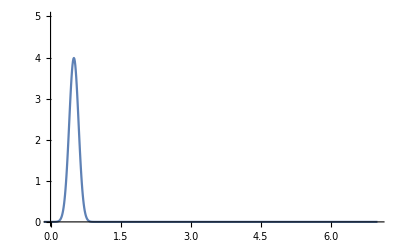

```mathematica
ListLinePlot[sdata1, PlotRange->{{0,7},{0,5}}]
```

### Basis function and creation of the bins of t

```mathematica
Clear[b]
b[En_, t_] = E^(-t*En)
```

ⅇ^(-En t)

```mathematica
Clear[Binst]
Binst = Table[Range[1, tmax, 1]];
```

```mathematica
Clear[NBins]
NBinsA = Dimensions[Binst];
NBins = NBinsA[[1]];
```

## Computation of the integrals for the evaluation of R, f, W^-1

```mathematica
Clean[RVec]
```

Clean[RVec]

```mathematica
Limit[Integrate[b[K, t],K], K-> Infinity] - Limit[Integrate[b[K, t],K], K-> Es]
```

ConditionalExpression[ⅇ^(-Es t)/t, t>0]

```mathematica
For[j=1, j<=NBins, j++, RVec[j] = Table[Integrate[b[K, j],{K, E0, Infinity}]]]
```

```mathematica
Table[RVec[i],{i,1,NBins}]
```

{0.904837,0.409365,0.246939,0.16758,0.121306,0.0914686,0.0709408,0.0561661,0.0451744,0.0367879,0.030261,0.0250995,0.020964,0.0176141,0.0148753,0.0126185,0.0107461,0.00918327,0.00787203,0.00676676,0.00583126,0.00503651,0.00435908,0.00377991,0.0032834,0.00285668,0.00248909,0.00217179,0.00189735,0.00165957,0.0014532}

```mathematica
Integrate[b[K,s]*b[K,t],{K, Es, Infinity}]
```

ConditionalExpression[ⅇ^(-Es (s+t))/(s+t), Re[s+t]>0]

```mathematica
Clear[WMatrix]
For[j=1, j<=NBins, j++,For[i=1,i<=NBins,i++, WMatrix[i,j] = Table[Integrate[b[K,i]*b[K,j],{K, E0, Infinity}]]]]
Clear[WM]
WM = Table[WMatrix[i,j],{i,1,NBins},{j,1,NBins}]
Clear[WMM1]
```

{{0.409365,0.246939,0.16758,0.121306,0.0914686,0.0709408,0.0561661,0.0451744,0.0367879,0.030261,0.0250995,0.020964,0.0176141,0.0148753,0.0126185,0.0107461,0.00918327,0.00787203,0.00676676,0.00583126,0.00503651,0.00435908,0.00377991,0.0032834,0.00285668,0.00248909,0.00217179,0.00189735,0.00165957,0.0014532,0.00127382},{0.246939,0.16758,0.121306,0.0914686,0.0709408,0.0561661,0.0451744,0.0367879,0.030261,0.0250995,0.020964,0.0176141,0.0148753,0.0126185,0.0107461,0.00918327,0.00787203,0.00676676,0.00583126,0.00503651,0.00435908,0.00377991,0.0032834,0.00285668,0.00248909,0.00217179,0.00189735,0.00165957,0.0014532,0.00127382,0.00111767},{0.16758,0.121306,0.0914686,0.0709408,0.0561661,0.0451744,0.0367879,0.030261,0.0250995,0.020964,0.0176141,0.0148753,0.0126185,0.0107461,0.00918327,0.00787203,0.00676676,0.00583126,0.00503651,0.00435908,0.00377991,0.0032834,0.00285668,0.00248909,0.00217179,0.00189735,0.00165957,0.0014532,0.00127382,0.00111767,0.000981567},{0.121306,0.0914686,0.0709408,0.0561661,0.0451744,0.0367879,0.030261,0.0250995,0.020964,0.0176141,0.0148753,0.0126185,0.0107461,0.00918327,0.00787203,0.00676676,0.00583126,0.00503651,0.00435908,0.00377991,0.0032834,0.00285668,0.00248909,0.00217179,0.00189735,0.00165957,0.0014532,0.00127382,0.00111767,0.000981567,0.000862782},{0.0914686,0.0709408,0.0561661,0.0451744,0.0367879,0.030261,0.0250995,0.020964,0.0176141,0.0148753,0.0126185,0.0107461,0.00918327,0.00787203,0.00676676,0.00583126,0.00503651,0.00435908,0.00377991,0.0032834,0.00285668,0.00248909,0.00217179,0.00189735,0.00165957,0.0014532,0.00127382,0.00111767,0.000981567,0.000862782,0.000758992},{0.0709408,0.0561661,0.0451744,0.0367879,0.030261,0.0250995,0.020964,0.0176141,0.0148753,0.0126185,0.0107461,0.00918327,0.00787203,0.00676676,0.00583126,0.00503651,0.00435908,0.00377991,0.0032834,0.00285668,0.00248909,0.00217179,0.00189735,0.00165957,0.0014532,0.00127382,0.00111767,0.000981567,0.000862782,0.000758992,0.000668203},{0.0561661,0.0451744,0.0367879,0.030261,0.0250995,0.020964,0.0176141,0.0148753,0.0126185,0.0107461,0.00918327,0.00787203,0.00676676,0.00583126,0.00503651,0.00435908,0.00377991,0.0032834,0.00285668,0.00248909,0.00217179,0.00189735,0.00165957,0.0014532,0.00127382,0.00111767,0.000981567,0.000862782,0.000758992,0.000668203,0.000588705},{0.0451744,0.0367879,0.030261,0.0250995,0.020964,0.0176141,0.0148753,0.0126185,0.0107461,0.00918327,0.00787203,0.00676676,0.00583126,0.00503651,0.00435908,0.00377991,0.0032834,0.00285668,0.00248909,0.00217179,0.00189735,0.00165957,0.0014532,0.00127382,0.00111767,0.000981567,0.000862782,0.000758992,0.000668203,0.000588705,0.000519023},{0.0367879,0.030261,0.0250995,0.020964,0.0176141,0.0148753,0.0126185,0.0107461,0.00918327,0.00787203,0.00676676,0.00583126,0.00503651,0.00435908,0.00377991,0.0032834,0.00285668,0.00248909,0.00217179,0.00189735,0.00165957,0.0014532,0.00127382,0.00111767,0.000981567,0.000862782,0.000758992,0.000668203,0.000588705,0.000519023,0.000457891},{0.030261,0.0250995,0.020964,0.0176141,0.0148753,0.0126185,0.0107461,0.00918327,0.00787203,0.00676676,0.00583126,0.00503651,0.00435908,0.00377991,0.0032834,0.00285668,0.00248909,0.00217179,0.00189735,0.00165957,0.0014532,0.00127382,0.00111767,0.000981567,0.000862782,0.000758992,0.000668203,0.000588705,0.000519023,0.000457891,0.000404212},{0.0250995,0.020964,0.0176141,0.0148753,0.0126185,0.0107461,0.00918327,0.00787203,0.00676676,0.00583126,0.00503651,0.00435908,0.00377991,0.0032834,0.00285668,0.00248909,0.00217179,0.00189735,0.00165957,0.0014532,0.00127382,0.00111767,0.000981567,0.000862782,0.000758992,0.000668203,0.000588705,0.000519023,0.000457891,0.000404212,0.000357038},{0.020964,0.0176141,0.0148753,0.0126185,0.0107461,0.00918327,0.00787203,0.00676676,0.00583126,0.00503651,0.00435908,0.00377991,0.0032834,0.00285668,0.00248909,0.00217179,0.00189735,0.00165957,0.0014532,0.00127382,0.00111767,0.000981567,0.000862782,0.000758992,0.000668203,0.000588705,0.000519023,0.000457891,0.000404212,0.000357038,0.000315548},{0.0176141,0.0148753,0.0126185,0.0107461,0.00918327,0.00787203,0.00676676,0.00583126,0.00503651,0.00435908,0.00377991,0.0032834,0.00285668,0.00248909,0.00217179,0.00189735,0.00165957,0.0014532,0.00127382,0.00111767,0.000981567,0.000862782,0.000758992,0.000668203,0.000588705,0.000519023,0.000457891,0.000404212,0.000357038,0.000315548,0.00027903},{0.0148753,0.0126185,0.0107461,0.00918327,0.00787203,0.00676676,0.00583126,0.00503651,0.00435908,0.00377991,0.0032834,0.00285668,0.00248909,0.00217179,0.00189735,0.00165957,0.0014532,0.00127382,0.00111767,0.000981567,0.000862782,0.000758992,0.000668203,0.000588705,0.000519023,0.000457891,0.000404212,0.000357038,0.000315548,0.00027903,0.000246867},{0.0126185,0.0107461,0.00918327,0.00787203,0.00676676,0.00583126,0.00503651,0.00435908,0.00377991,0.0032834,0.00285668,0.00248909,0.00217179,0.00189735,0.00165957,0.0014532,0.00127382,0.00111767,0.000981567,0.000862782,0.000758992,0.000668203,0.000588705,0.000519023,0.000457891,0.000404212,0.000357038,0.000315548,0.00027903,0.000246867,0.000218518},{0.0107461,0.00918327,0.00787203,0.00676676,0.00583126,0.00503651,0.00435908,0.00377991,0.0032834,0.00285668,0.00248909,0.00217179,0.00189735,0.00165957,0.0014532,0.00127382,0.00111767,0.000981567,0.000862782,0.000758992,0.000668203,0.000588705,0.000519023,0.000457891,0.000404212,0.000357038,0.000315548,0.00027903,0.000246867,0.000218518,0.000193517},{0.00918327,0.00787203,0.00676676,0.00583126,0.00503651,0.00435908,0.00377991,0.0032834,0.00285668,0.00248909,0.00217179,0.00189735,0.00165957,0.0014532,0.00127382,0.00111767,0.000981567,0.000862782,0.000758992,0.000668203,0.000588705,0.000519023,0.000457891,0.000404212,0.000357038,0.000315548,0.00027903,0.000246867,0.000218518,0.000193517,0.000171453},{0.00787203,0.00676676,0.00583126,0.00503651,0.00435908,0.00377991,0.0032834,0.00285668,0.00248909,0.00217179,0.00189735,0.00165957,0.0014532,0.00127382,0.00111767,0.000981567,0.000862782,0.000758992,0.000668203,0.000588705,0.000519023,0.000457891,0.000404212,0.000357038,0.000315548,0.00027903,0.000246867,0.000218518,0.000193517,0.000171453,0.000151971},{0.00676676,0.00583126,0.00503651,0.00435908,0.00377991,0.0032834,0.00285668,0.00248909,0.00217179,0.00189735,0.00165957,0.0014532,0.00127382,0.00111767,0.000981567,0.000862782,0.000758992,0.000668203,0.000588705,0.000519023,0.000457891,0.000404212,0.000357038,0.000315548,0.00027903,0.000246867,0.000218518,0.000193517,0.000171453,0.000151971,0.000134759},{0.00583126,0.00503651,0.00435908,0.00377991,0.0032834,0.00285668,0.00248909,0.00217179,0.00189735,0.00165957,0.0014532,0.00127382,0.00111767,0.000981567,0.000862782,0.000758992,0.000668203,0.000588705,0.000519023,0.000457891,0.000404212,0.000357038,0.000315548,0.00027903,0.000246867,0.000218518,0.000193517,0.000171453,0.000151971,0.000134759,0.000119544},{0.00503651,0.00435908,0.00377991,0.0032834,0.00285668,0.00248909,0.00217179,0.00189735,0.00165957,0.0014532,0.00127382,0.00111767,0.000981567,0.000862782,0.000758992,0.000668203,0.000588705,0.000519023,0.000457891,0.000404212,0.000357038,0.000315548,0.00027903,0.000246867,0.000218518,0.000193517,0.000171453,0.000151971,0.000134759,0.000119544,0.000106088},{0.00435908,0.00377991,0.0032834,0.00285668,0.00248909,0.00217179,0.00189735,0.00165957,0.0014532,0.00127382,0.00111767,0.000981567,0.000862782,0.000758992,0.000668203,0.000588705,0.000519023,0.000457891,0.000404212,0.000357038,0.000315548,0.00027903,0.000246867,0.000218518,0.000193517,0.000171453,0.000151971,0.000134759,0.000119544,0.000106088,0.000094181},{0.00377991,0.0032834,0.00285668,0.00248909,0.00217179,0.00189735,0.00165957,0.0014532,0.00127382,0.00111767,0.000981567,0.000862782,0.000758992,0.000668203,0.000588705,0.000519023,0.000457891,0.000404212,0.000357038,0.000315548,0.00027903,0.000246867,0.000218518,0.000193517,0.000171453,0.000151971,0.000134759,0.000119544,0.000106088,0.000094181,0.0000836404},{0.0032834,0.00285668,0.00248909,0.00217179,0.00189735,0.00165957,0.0014532,0.00127382,0.00111767,0.000981567,0.000862782,0.000758992,0.000668203,0.000588705,0.000519023,0.000457891,0.000404212,0.000357038,0.000315548,0.00027903,0.000246867,0.000218518,0.000193517,0.000171453,0.000151971,0.000134759,0.000119544,0.000106088,0.000094181,0.0000836404,0.0000743049},{0.00285668,0.00248909,0.00217179,0.00189735,0.00165957,0.0014532,0.00127382,0.00111767,0.000981567,0.000862782,0.000758992,0.000668203,0.000588705,0.000519023,0.000457891,0.000404212,0.000357038,0.000315548,0.00027903,0.000246867,0.000218518,0.000193517,0.000171453,0.000151971,0.000134759,0.000119544,0.000106088,0.000094181,0.0000836404,0.0000743049,0.0000660333},{0.00248909,0.00217179,0.00189735,0.00165957,0.0014532,0.00127382,0.00111767,0.000981567,0.000862782,0.000758992,0.000668203,0.000588705,0.000519023,0.000457891,0.000404212,0.000357038,0.000315548,0.00027903,0.000246867,0.000218518,0.000193517,0.000171453,0.000151971,0.000134759,0.000119544,0.000106088,0.000094181,0.0000836404,0.0000743049,0.0000660333,0.0000587011},{0.00217179,0.00189735,0.00165957,0.0014532,0.00127382,0.00111767,0.000981567,0.000862782,0.000758992,0.000668203,0.000588705,0.000519023,0.000457891,0.000404212,0.000357038,0.000315548,0.00027903,0.000246867,0.000218518,0.000193517,0.000171453,0.000151971,0.000134759,0.000119544,0.000106088,0.000094181,0.0000836404,0.0000743049,0.0000660333,0.0000587011,0.0000521992},{0.00189735,0.00165957,0.0014532,0.00127382,0.00111767,0.000981567,0.000862782,0.000758992,0.000668203,0.000588705,0.000519023,0.000457891,0.000404212,0.000357038,0.000315548,0.00027903,0.000246867,0.000218518,0.000193517,0.000171453,0.000151971,0.000134759,0.000119544,0.000106088,0.000094181,0.0000836404,0.0000743049,0.0000660333,0.0000587011,0.0000521992,0.0000464313},{0.00165957,0.0014532,0.00127382,0.00111767,0.000981567,0.000862782,0.000758992,0.000668203,0.000588705,0.000519023,0.000457891,0.000404212,0.000357038,0.000315548,0.00027903,0.000246867,0.000218518,0.000193517,0.000171453,0.000151971,0.000134759,0.000119544,0.000106088,0.000094181,0.0000836404,0.0000743049,0.0000660333,0.0000587011,0.0000521992,0.0000464313,0.0000413125},{0.0014532,0.00127382,0.00111767,0.000981567,0.000862782,0.000758992,0.000668203,0.000588705,0.000519023,0.000457891,0.000404212,0.000357038,0.000315548,0.00027903,0.000246867,0.000218518,0.000193517,0.000171453,0.000151971,0.000134759,0.000119544,0.000106088,0.000094181,0.0000836404,0.0000743049,0.0000660333,0.0000587011,0.0000521992,0.0000464313,0.0000413125,0.0000367683},{0.00127382,0.00111767,0.000981567,0.000862782,0.000758992,0.000668203,0.000588705,0.000519023,0.000457891,0.000404212,0.000357038,0.000315548,0.00027903,0.000246867,0.000218518,0.000193517,0.000171453,0.000151971,0.000134759,0.000119544,0.000106088,0.000094181,0.0000836404,0.0000743049,0.0000660333,0.0000587011,0.0000521992,0.0000464313,0.0000413125,0.0000367683,0.0000327328}}

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.409365,0.246939,0.16758,0.121306,0.0914686,0.0709408,0.0561661,0.0451744,0.0367879,0.030261,«21»},{0.246939,0.16758,0.121306,0.0914686,0.0709408,0.0561661,0.0451744,0.0367879,0.030261,0.0250995,«21»},«8»,«21»} may contain significant numerical errors.

```mathematica
WMM1 = Inverse[Rationalize[WM]]
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.409365,0.246939,0.16758,0.121306,0.0914686,0.0709408,0.0561661,0.0451744,0.0367879,0.030261,«21»},{0.246939,0.16758,0.121306,0.0914686,0.0709408,0.0561661,0.0451744,0.0367879,0.030261,0.0250995,«21»},«8»,«21»} may contain significant numerical errors.

{{17033.,-1.04964×10^6,2.36419×10^7,-2.70667×10^8,1.79733×10^9,-7.33953×10^9,1.86711×10^10,-2.85739×10^10,2.31221×10^10,-5.21761×10^9,-5.01598×10^9,6.40338×10^9,-5.59714×10^9,-3.58203×10^9,3.60403×10^9,4.98195×10^9,8.71809×10^9,-1.43359×10^10,9.82711×10^9,-2.2246×10^10,5.22852×10^9,5.69246×10^9,1.42673×10^10,-6.50385×10^9,1.7274×10^10,-3.06547×10^10,1.62317×10^10,-2.71646×10^10,6.41465×10^9,3.38368×10^10,-1.9597×10^10},{-1.04821×10^6,7.37156×10^7,-1.79629×10^9,2.17232×10^10,-1.50446×10^11,6.36005×10^11,-1.66757×10^12,2.62399×10^12,-2.18166×10^12,5.0969×10^11,4.72612×10^11,-5.71523×10^11,5.23236×10^11,2.98527×10^11,-3.66468×10^11,-4.87036×10^11,-7.46153×10^11,1.34655×10^12,-8.46977×10^11,2.05791×10^12,-5.61395×10^11,-6.21135×10^11,-1.30804×10^12,6.19971×10^11,-1.50545×10^12,2.84923×10^12,-1.46553×10^12,2.49688×10^12,-7.23211×10^11,-3.10059×10^12,1.84916×10^12},{2.35548×10^7,-1.7922×10^9,4.61143×10^10,-5.81133×10^11,4.16064×10^12,-1.80913×10^13,4.86309×10^13,-7.82993×10^13,6.65289×10^13,-1.58755×10^13,-1.45091×10^13,1.64976×10^13,-1.56879×10^13,-7.95123×10^12,1.18171×10^13,1.50879×10^13,2.07446×10^13,-4.09386×10^13,2.38716×10^13,-6.15766×10^13,1.90332×10^13,2.10751×10^13,3.8808×10^13,-1.95213×10^13,4.28845×10^13,-8.57961×10^13,4.3248×10^13,-7.41247×10^13,2.47313×10^13,9.20138×10^13,-5.62445×10^13},{-2.68772×10^8,2.16047×10^10,-5.79327×10^11,7.54453×10^12,-5.55109×10^13,2.47124×10^14,-6.78379×10^14,1.1134×10^15,-9.62534×10^14,2.31713×10^14,2.12726×10^14,-2.24994×10^14,2.21542×10^14,9.81283×10^13,-1.78423×10^14,-2.18534×10^14,-2.73757×10^14,5.90595×10^14,-3.21955×10^14,8.74465×10^14,-3.01688×10^14,-3.31935×10^14,-5.46527×10^14,2.97378×10^14,-5.84744×10^14,1.22724×10^15,-6.11019×10^14,1.042×10^15,-3.86488×10^14,-1.29563×10^15,8.09128×10^14},{1.77677×10^9,-1.48995×10^11,4.13099×10^12,-5.52921×10^13,4.16374×10^14,-1.89142×10^15,5.28633×10^15,-8.81733×10^15,7.72438×10^15,-1.85044×10^15,-1.73965×10^15,1.68209×10^15,-1.72264×10^15,-6.39695×10^14,1.48188×10^15,1.73421×10^15,1.99221×10^15,-4.72228×10^15,2.42074×10^15,-6.88877×10^15,2.63064×10^15,2.86765×10^15,4.27243×10^15,-2.56561×10^15,4.4526×10^15,-9.74242×10^15,4.82292×10^15,-8.09132×10^15,3.27067×10^15,1.00963×10^16,-6.4311×10^15},{-7.21224×10^9,6.2636×10^11,-1.78674×10^13,2.44894×10^14,-1.88193×10^15,8.70118×10^15,-2.47×10^16,4.17519×10^16,-3.69032×10^16,8.63657×10^15,8.50422×10^15,-7.29055×10^15,7.918×10^15,2.21438×10^15,-7.30614×10^15,-8.10236×10^15,-8.48218×10^15,2.24407×10^16,-1.08354×10^16,3.23098×10^16,-1.36235×10^16,-1.47198×10^16,-1.99484×10^16,1.35304×10^16,-2.02726×10^16,4.60506×10^16,-2.2773×10^16,3.71009×10^16,-1.62456×10^16,-4.65535×10^16,3.02651×10^16},{1.81915×10^10,-1.6293×10^12,4.76706×10^13,-6.67435×10^14,5.22298×10^15,-2.45288×10^16,7.05597×10^16,-1.20492×10^17,1.06803×10^17,-2.36846×10^16,-2.51735×10^16,1.79615×10^16,-2.19751×10^16,-3.12918×10^15,2.19651×10^16,2.27478×10^16,2.08837×10^16,-6.4397×10^16,2.90757×10^16,-9.18959×10^16,4.29549×10^16,4.62267×10^16,5.71152×10^16,-4.49757×10^16,5.59066×10^16,-1.31873×10^17,6.51099×10^16,-1.01368×10^17,4.8894×10^16,1.28204×10^17,-8.55562×10^16},{-2.74441×10^10,2.52972×10^12,-7.57845×10^13,1.08211×10^15,-8.60803×10^15,4.09745×10^16,-1.19077×10^17,2.04364×10^17,-1.79623×10^17,3.54095×10^16,4.2444×10^16,-2.09388×10^16,3.6127×10^16,-3.66047×10^15,-3.95177×10^16,-3.75319×10^16,-2.54456×10^16,1.06577×10^17,-4.3475×10^16,1.52749×10^17,-8.02138×10^16,-8.71528×10^16,-9.93356×10^16,9.33164×10^16,-8.82759×10^16,2.19367×10^17,-1.06076×10^17,1.54978×10^17,-8.92657×10^16,-1.97415×10^17,1.3837×10^17},{2.14265×10^10,-2.03364×10^12,6.23524×10^13,-9.0672×10^14,7.31307×10^15,-3.51261×10^16,1.02341×10^17,-1.7404×10^17,1.46928×10^17,-2.11234×10^16,-2.95633×10^16,-1.61525×10^15,-3.38516×10^16,2.00052×10^16,3.84332×10^16,3.51207×10^16,4.09154×10^14,-8.29331×10^16,2.51458×10^16,-1.27491×10^17,7.7833×10^16,8.81379×10^16,1.01476×10^17,-1.12052×10^17,6.06563×10^16,-1.75574×10^17,7.28116×10^16,-1.0244×10^17,1.00139×10^17,1.24106×10^17,-1.04269×10^17},{-3.45827×10^9,3.49753×10^11,-1.1143×10^13,1.64882×10^14,-1.32415×10^15,6.15627×10^15,-1.65635×10^16,2.3458×10^16,-1.14033×10^16,-1.95416×10^15,-1.76207×10^16,2.49328×10^16,2.13725×10^16,-2.53168×10^16,-1.04931×10^16,-2.54487×10^16,3.73754×10^16,-3.64689×10^15,1.4371×10^16,2.20418×10^16,-1.96874×10^16,-2.27148×10^16,-6.2488×10^16,5.57329×10^16,2.23115×10^16,-9.96495×10^14,3.11884×10^16,-4.85588×10^15,-8.50368×10^16,5.09839×10^16,-5.08399×10^14},{-6.6112×10^9,6.18377×10^11,-1.88586×10^13,2.74816×10^14,-2.23525×10^15,1.08829×10^16,-3.2207×10^16,5.49969×10^16,-4.193×10^16,-1.25209×10^16,3.68603×10^16,-1.20119×10^15,-1.72418×10^16,8.32572×10^15,-2.34647×10^16,3.35279×10^16,-3.8963×10^16,4.12373×10^16,-1.58664×10^16,2.53773×10^16,-1.47134×10^16,-4.81921×10^16,2.6856×10^16,2.92248×10^16,-6.41099×10^16,9.48088×10^16,-5.24812×10^16,-2.14522×10^16,7.51247×10^16,-8.41865×10^16,3.33004×10^16},{7.65608×10^9,-6.84504×10^11,1.98193×10^13,-2.71601×10^14,2.0464×10^15,-8.99306×10^15,2.2816×10^16,-2.91513×10^16,5.80395×10^15,2.22409×10^16,-7.64635×10^14,-2.78667×10^16,3.17356×10^15,-9.26723×10^15,5.09024×10^16,-2.66414×10^16,1.42872×10^16,-2.0367×10^16,-1.11639×10^16,-1.48624×10^16,-1.17391×10^16,6.71473×10^16,2.77946×10^16,-6.58912×10^16,5.07859×10^16,-5.8054×10^16,-4.92979×10^16,8.03861×10^16,-1.25182×10^16,1.82897×10^16,-1.8862×10^16},{-6.03025×10^9,5.66752×10^11,-1.70943×10^13,2.4303×10^14,-1.90447×10^15,8.83598×10^15,-2.48093×10^16,4.13719×10^16,-3.92153×10^16,2.40379×10^16,-1.87509×10^16,5.17101×10^15,6.08247×10^15,3.88546×10^16,-5.13126×10^16,-1.00328×10^16,-2.86227×10^15,2.1453×10^16,5.78037×10^15,2.7658×10^16,1.86474×10^16,-3.35234×10^16,-8.68575×10^16,6.7245×10^16,-3.59085×10^16,7.60588×10^15,8.125×10^16,2.86504×10^16,-7.29177×10^16,-5.90559×10^16,5.43082×10^16},{-3.05079×10^9,2.43619×10^11,-6.14155×10^12,7.0026×10^13,-3.98018×10^14,9.71727×10^14,7.93984×10^14,-1.11058×10^16,2.76484×10^16,-2.80203×10^16,7.18089×10^15,-8.74874×10^15,3.81956×10^16,-3.27227×10^16,1.69372×10^15,5.61763×10^15,-1.21946×10^16,1.18646×10^16,-7.79535×10^15,2.6217×10^16,1.78266×10^15,-4.93942×10^16,4.87348×10^16,-3.4118×10^16,-4.08415×10^16,9.54488×10^16,-5.90614×10^15,-5.06283×10^16,1.61875×10^15,1.82051×10^16,-4.16226×10^15},{2.01531×10^9,-2.17555×10^11,7.29848×10^12,-1.13276×10^14,9.59984×10^14,-4.81022×10^15,1.46923×10^16,-2.70162×10^16,2.73819×10^16,-8.09444×10^15,-2.09631×10^16,4.85265×10^16,-4.66277×10^16,-1.07723×10^15,1.9505×10^16,6.39746×10^15,1.89799×10^16,-4.34104×10^16,3.43336×10^16,-4.25973×10^16,-3.00201×10^16,8.19071×10^16,-2.86012×10^15,-5.81739×10^16,1.10442×10^17,-7.04658×10^16,-2.38624×10^16,-5.26577×10^16,5.61659×10^16,6.1108×10^16,-4.7679×10^16},{5.30759×10^9,-5.22399×10^11,1.62965×10^13,-2.37778×10^14,1.90241×10^15,-8.97649×10^15,2.55418×10^16,-4.30354×10^16,4.17335×10^16,-3.07244×10^16,3.7614×10^16,-2.89098×10^16,-1.1389×10^16,5.40623×10^15,1.05683×10^16,2.61732×10^16,-1.36625×10^16,1.25175×10^15,-9.99542×10^15,-7.9615×10^16,8.17111×10^16,-2.49172×10^15,-2.17503×10^16,9.63769×10^16,-2.00569×10^16,-9.20189×10^16,-6.14182×10^15,-1.23034×10^16,5.6319×10^16,3.87469×10^16,-4.20784×10^16},{1.06607×10^10,-9.22936×10^11,2.59862×10^13,-3.47925×10^14,2.57688×10^15,-1.12354×10^16,2.87632×10^16,-3.86141×10^16,1.1325×10^16,3.575×10^16,-4.06039×10^16,1.36228×10^16,-5.85839×10^15,-9.27752×10^15,2.07035×10^16,-1.08894×10^16,4.63512×10^16,-4.33284×10^16,-2.82714×10^16,3.0985×10^16,-1.9728×10^16,-4.48053×10^16,1.35964×10^17,-3.14754×10^16,-1.51605×10^16,-8.03678×10^16,5.02311×10^16,-1.42651×10^16,-3.18907×10^14,5.0687×10^16,-3.24522×10^16},{-1.54331×10^10,1.45075×10^12,-4.41838×10^13,6.39054×10^14,-5.12753×10^15,2.44831×10^16,-7.07651×10^16,1.18683×10^17,-9.60601×10^16,3.55419×10^15,3.81907×10^16,-1.73313×10^16,2.19222×10^16,1.18942×10^16,-4.95496×10^16,1.40412×10^15,-3.70186×10^16,4.43161×10^16,4.07605×10^16,7.84892×10^16,-1.24112×10^17,4.5448×10^16,-8.93061×10^16,1.56232×10^16,-8.10416×10^16,1.92334×10^17,-5.19614×10^16,1.10538×10^17,-8.2434×10^16,-1.56452×10^17,1.12983×10^17},{8.65409×10^9,-7.41706×10^11,2.08144×10^13,-2.79835×10^14,2.09968×10^15,-9.38884×10^15,2.51967×10^16,-3.77297×10^16,2.19254×10^16,1.23636×10^16,-1.34074×10^16,-1.11666×10^16,7.43663×10^15,-9.95819×10^15,3.53645×10^16,-1.21961×10^16,-3.15392×10^16,4.68642×10^16,-1.32606×10^16,-1.05052×10^17,1.27294×10^17,1.14945×10^15,-5.38526×10^15,-8.17774×10^16,7.03239×10^16,-3.03397×10^16,3.26246×10^16,-3.91757×10^16,-1.64782×10^15,4.06641×10^16,-2.10319×10^16},{-2.02929×10^10,1.89175×10^12,-5.69705×10^13,8.13521×10^14,-6.44005×10^15,3.03466×10^16,-8.67741×10^16,1.45523×10^17,-1.24864×10^17,2.95486×10^16,1.349×10^16,-7.79115×10^15,2.41149×10^16,3.3119×10^16,-5.44997×10^16,-7.36364×10^16,4.20437×10^16,6.69293×10^16,-1.07647×10^17,2.36683×10^17,-6.96962×10^16,-9.43873×10^16,-1.52252×10^17,1.112×10^17,-5.4284×10^16,1.89704×10^17,-8.10724×10^16,1.20186×10^17,-8.65679×10^16,-1.64281×10^17,1.20611×10^17},{5.4364×10^9,-5.91114×10^11,2.01837×10^13,-3.21177×10^14,2.80577×10^15,-1.45378×10^16,4.58338×10^16,-8.57045×10^16,8.42405×10^16,-2.52664×10^16,-9.2326×10^15,-1.49582×10^16,1.80738×10^16,-3.60843×10^15,-1.85965×10^16,8.07655×10^16,-2.58217×10^16,-1.21612×10^17,1.28518×10^17,-7.87351×10^16,2.57918×10^16,-1.11059×10^16,9.58172×10^16,-6.64552×10^16,4.91767×10^16,-1.00632×10^17,3.68871×10^16,-5.32821×10^16,5.13727×10^16,6.39081×10^16,-5.33812×10^16},{2.80598×10^9,-3.58248×10^11,1.33172×10^13,-2.23187×10^14,2.02245×10^15,-1.08204×10^16,3.54147×10^16,-7.01177×10^16,7.63341×10^16,-2.53417×10^16,-4.08878×10^16,6.33662×10^16,-2.67386×10^16,-5.3503×10^16,8.13827×10^16,-6.2772×10^15,-5.33318×10^16,5.78272×10^16,4.79581×10^15,-8.40934×10^16,-2.32711×10^16,8.7838×10^16,1.12614×10^16,1.65548×10^16,2.67181×10^16,-1.06269×10^17,4.86036×10^16,-1.00421×10^17,3.98192×10^16,1.33873×10^17,-8.45664×10^16},{1.48784×10^10,-1.36919×10^12,4.08144×10^13,-5.78043×10^14,4.5493×10^15,-2.14133×10^16,6.19097×10^16,-1.08905×10^17,1.12369×10^17,-6.88855×10^16,3.0669×10^16,2.20963×10^16,-8.53106×10^16,5.10306×10^16,3.17776×10^15,-2.87546×10^16,1.32949×10^17,-8.77593×10^16,-1.81314×10^15,-1.5525×10^17,9.21895×10^16,2.421×10^16,1.08013×10^17,-7.71656×10^15,1.64207×10^16,-1.35845×10^17,2.76121×10^16,-1.42431×10^17,1.27384×10^17,1.44088×10^17,-1.141×10^17},{-4.22966×10^9,4.11994×10^11,-1.33958×10^13,2.12192×10^14,-1.91354×10^15,1.0599×10^16,-3.72074×10^16,8.21684×10^16,-1.06565×10^17,6.07177×10^16,2.31408×10^16,-6.21119×10^16,5.96848×10^16,-3.18057×10^16,-5.664×10^16,1.03045×10^17,-2.56249×10^16,2.07086×10^15,-8.2561×10^16,1.01156×10^17,-5.72588×10^16,1.782×10^16,5.91884×10^15,1.92757×10^16,-3.83989×10^16,2.68915×10^16,-8.56509×10^16,1.20877×10^17,-2.91739×10^15,-8.27359×10^16,3.78376×10^16},{1.729×10^10,-1.50729×10^12,4.29617×10^13,-5.86255×10^14,4.46867×10^15,-2.03763×10^16,5.63517×10^16,-8.96576×10^16,6.39329×10^16,1.64884×10^16,-5.72025×10^16,4.63686×10^16,-3.42866×10^16,-4.39979×10^16,1.14057×10^17,-1.75955×10^16,-2.24801×10^16,-7.58519×10^16,7.14975×10^16,-5.90773×10^16,4.81759×10^16,3.13644×10^16,1.82838×10^16,-4.39729×10^16,-3.53621×10^15,-7.90472×10^16,8.71606×10^16,9.15101×10^15,-2.44467×10^16,1.17529×10^16,-6.99002×10^15},{-3.36915×10^10,3.1427×10^12,-9.49753×10^13,1.36357×10^15,-1.08676×10^16,5.1604×10^16,-1.4868×10^17,2.50011×10^17,-2.06938×10^17,1.5448×10^16,8.62767×10^16,-5.06078×10^16,1.03964×10^16,1.00505×10^17,-9.05068×10^16,-9.692×10^16,-6.37282×10^16,1.95949×10^17,-4.40382×10^16,2.21873×10^17,-1.05689×10^17,-1.42744×10^17,-1.46244×10^17,6.18581×10^16,-9.15807×10^16,3.3329×10^17,-4.51908×10^16,1.5959×10^17,-2.23416×10^17,-2.13954×10^17,1.93151×10^17},{1.87755×10^10,-1.70689×10^12,5.07004×10^13,-7.20823×10^14,5.72614×10^15,-2.72387×10^16,7.87231×10^16,-1.31174×10^17,9.83717×10^16,2.06844×10^16,-5.37187×10^16,-4.78391×10^16,7.9519×10^16,-1.06747×10^16,-1.36182×10^16,-2.27071×10^15,4.54847×10^16,-5.8423×10^16,4.16289×10^16,-1.06687×10^17,4.89185×10^16,6.75221×10^16,2.84937×10^16,-9.92147×10^16,1.00993×10^17,-6.00534×10^16,2.1162×10^16,-1.71293×10^17,1.30016×10^17,9.59037×10^16,-8.03122×10^16},{-2.68976×10^10,2.47887×10^12,-7.37996×10^13,1.04058×10^15,-8.10747×10^15,3.73263×10^16,-1.02584×10^17,1.58671×10^17,-1.09491×10^17,4.41179×10^15,-3.0873×10^16,8.79061×10^16,2.39552×10^16,-4.38788×10^16,-6.51711×10^16,-4.20476×10^15,-1.03085×10^16,1.04628×10^17,-4.08502×10^16,1.25511×10^17,-5.02121×10^16,-1.1164×10^17,-1.39664×10^17,1.26559×10^17,1.22711×10^16,1.4169×10^17,-1.54288×10^17,2.01499×10^17,-1.18761×10^17,-1.54031×10^17,1.18736×10^17},{5.09919×10^9,-6.12031×10^11,2.16795×10^13,-3.4661×10^14,2.98126×10^15,-1.49981×10^16,4.56773×10^16,-8.47199×10^16,9.8337×10^16,-8.99414×10^16,8.4933×10^16,-2.12167×10^16,-6.94203×10^16,-7.51548×10^14,6.63913×10^16,4.63327×10^16,-6.23687×10^15,-7.39258×10^16,-1.09311×10^15,-8.14536×10^16,3.94095×10^16,5.0196×10^16,1.27574×10^17,-1.45923×10^16,-3.19727×10^16,-1.95208×10^17,1.14032×10^17,-1.1468×10^17,1.31693×10^17,8.10579×10^16,-8.81457×10^16},{3.39069×10^10,-3.10942×10^12,9.23774×10^13,-1.3025×10^15,1.01663×10^16,-4.69762×10^16,1.29804×10^17,-2.01382×10^17,1.30966×10^17,4.1735×10^16,-7.37605×10^16,9.9398×10^15,-5.479×10^16,1.18939×10^16,7.18276×10^16,3.58516×10^16,4.27496×10^16,-1.51126×10^17,4.46332×10^16,-1.72072×10^17,6.11445×10^16,1.47329×10^17,1.41699×10^17,-9.05936×10^16,9.7777×10^15,-1.97243×10^17,7.67775×10^16,-1.49782×10^17,8.62253×10^16,2.71864×10^17,-1.85542×10^17},{-1.92882×10^10,1.82525×10^12,-5.56727×10^13,8.03086×10^14,-6.40064×10^15,3.02128×10^16,-8.5747×10^16,1.39698×10^17,-1.08004×10^17,6.18806×10^15,2.47694×10^16,-1.17856×10^16,5.10598×10^16,-6.56615×10^13,-5.66377×10^16,-3.8036×10^16,-2.55613×10^16,1.07598×10^17,-2.40077×10^16,1.23969×10^17,-4.82702×10^16,-9.60262×10^16,-1.12726×10^17,4.68169×10^16,-4.26254×10^15,1.755×10^17,-6.50344×10^16,1.15267×10^17,-9.12533×10^16,-1.83761×10^17,1.3583×10^17}}

```mathematica
Dimensions[WMM1];
```

```mathematica
For[j=1, j<=NBins, j++,fVec[j]=0];
For[j=1, j<=NBins, j++, fVec[j] = Table[Limit[Integrate[b[K, j]*DeltaS[K],K], K-> Infinity]-  Limit[Integrate[b[K, j]*DeltaS[K],K], K-> E0]]; Print[fVec[j]]]
```

0.609542

0.375284

0.233375

0.146584

0.0929929

0.0595859

0.0385622

0.0252057

0.0166396

0.011094

0.00746995

0.00507942

0.00348784

0.00241835

0.00169304

0.00119665

0.000853827

0.000614931

0.000446967

0.000327831

0.00024259

0.000181076

0.000136309

0.000103457

0.0000791518

0.0000610264

0.0000474036

0.0000370869

0.0000292159

0.0000231677

0.0000184875

## Evaluation of the coefficients g_t and plot as a function of t

### Computation of g_t for each Bin of t as the combination of three terms

```mathematica
For[j=1, j<=NBins, j++,g1[j]=0];
For[j=1, j<=NBins, j++,For[i=1,i<=NBins,i++, g1[j] = g1[j] +fVec[i]*WMM1[[j,i]]]; Print[N[g1[j],10]]]
```

0.0918606

-42.8252

2356.3

-49711.8

530076.

-3.20231×10^6

1.14284×10^7

-2.37097×10^7

2.56055×10^7

-8.48222×10^6

-5.84783×10^6

5.70861×10^6

-8.47667×10^6

1.25172×10^6

7.9973×10^6

9.447×10^6

2.20445×10^6

-2.11781×10^7

695867.

-2.0877×10^7

1.73603×10^7

1.58856×10^7

1.67246×10^7

-4.84849×10^6

1.66551×10^6

-4.03694×10^7

1.25188×10^7

-2.32389×10^7

2.65965×10^7

3.16582×10^7

-2.70159×10^7

```mathematica
For[j=1, j<=NBins, j++,g1[j]=0];
For[j=1, j<=NBins, j++,For[i=1,i<=NBins,i++, g1[j] = g1[j] +fVec[i]*WMM1[[j,i]]]]
```

```mathematica
For[j=1, j<=NBins, j++,g2A[j]=0]
For[j=1, j<=NBins, j++,For[i=1,i<=NBins,i++, g2A[j] = g2A[j] +RVec[i]*WMM1[[j,i]]]]
```

```mathematica
g2NScal=0;
For[j=1, j<=NBins, j++,For[i=1,i<=NBins,i++, g2NScal = g2NScal+(RVec[j]*fVec[i])*WMM1[[j,i]]]]
```

```mathematica
N[g2NScal,10];
```

```mathematica
g2DScal = 0;
For[j=1, j<=NBins, j++,For[i=1,i<=NBins,i++, g2DScal = g2DScal+(RVec[j]*RVec[i])*WMM1[[j,i]]]]
N[g2DScal]
```

6.39197

```mathematica
Clear[qFin]
For[j=1, j<=NBins, j++, qFin[j] = g1[j] + g2A[j]*g2NScal/g2DScal]
```

```mathematica
Print[Table[qFin[i],{i,1,NBins}]]
```

{27.7474,-1301.23,27126.2,-310714.,2.1608×10^6,-9.53323×10^6,2.67975×10^7,-4.60861×10^7,4.24394×10^7,-1.09416×10^7,-1.1184×10^7,1.21349×10^7,-1.32236×10^7,-1.56739×10^6,9.30387×10^6,1.33512×10^7,1.14868×10^7,-3.3491×10^7,8.35473×10^6,-3.7113×10^7,2.09206×10^7,1.71343×10^7,2.88387×10^7,-8.23636×10^6,1.66836×10^7,-6.74369×10^7,2.8142×10^7,-4.50186×10^7,2.91658×10^7,5.93722×10^7,-4.21886×10^7}

### Plot of g_t for each bin of t

```mathematica
Clear[qPlot]
qPlot = Table[qFin[j], {j,1,NBins}]
```

{27.7474,-1301.23,27126.2,-310714.,2.1608×10^6,-9.53323×10^6,2.67975×10^7,-4.60861×10^7,4.24394×10^7,-1.09416×10^7,-1.1184×10^7,1.21349×10^7,-1.32236×10^7,-1.56739×10^6,9.30387×10^6,1.33512×10^7,1.14868×10^7,-3.3491×10^7,8.35473×10^6,-3.7113×10^7,2.09206×10^7,1.71343×10^7,2.88387×10^7,-8.23636×10^6,1.66836×10^7,-6.74369×10^7,2.8142×10^7,-4.50186×10^7,2.91658×10^7,5.93722×10^7,-4.21886×10^7}

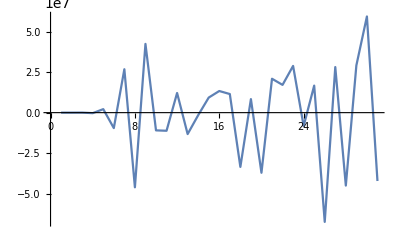

```mathematica
output1 = ListLinePlot[Transpose@{Binst, qPlot}]
```

```mathematica
Export["/Users/manuel/Documents/GitHub/Conducibility/Programmi/Delta_3.10.png",output1]
```

/Users/manuel/Documents/GitHub/Conducibility/Programmi/Delta_3.10.png

## Computation of DeltaBar and comparison with the target function

```mathematica
DeltaBar[Om_] = Sum[qFin[i]*b[Om,i],{i,NBins}]
```

-4.21886×10^7 ⅇ^(-31 Om)+5.93722×10^7 ⅇ^(-30 Om)+2.91658×10^7 ⅇ^(-29 Om)-4.50186×10^7 ⅇ^(-28 Om)+2.8142×10^7 ⅇ^(-27 Om)-6.74369×10^7 ⅇ^(-26 Om)+1.66836×10^7 ⅇ^(-25 Om)-8.23636×10^6 ⅇ^(-24 Om)+2.88387×10^7 ⅇ^(-23 Om)+1.71343×10^7 ⅇ^(-22 Om)+2.09206×10^7 ⅇ^(-21 Om)-3.7113×10^7 ⅇ^(-20 Om)+8.35473×10^6 ⅇ^(-19 Om)-3.3491×10^7 ⅇ^(-18 Om)+1.14868×10^7 ⅇ^(-17 Om)+1.33512×10^7 ⅇ^(-16 Om)+9.30387×10^6 ⅇ^(-15 Om)-1.56739×10^6 ⅇ^(-14 Om)-1.32236×10^7 ⅇ^(-13 Om)+1.21349×10^7 ⅇ^(-12 Om)-1.1184×10^7 ⅇ^(-11 Om)-1.09416×10^7 ⅇ^(-10 Om)+4.24394×10^7 ⅇ^(-9 Om)-4.60861×10^7 ⅇ^(-8 Om)+2.67975×10^7 ⅇ^(-7 Om)-9.53323×10^6 ⅇ^(-6 Om)+2.1608×10^6 ⅇ^(-5 Om)-310714. ⅇ^(-4 Om)+27126.2 ⅇ^(-3 Om)-1301.23 ⅇ^(-2 Om)+27.7474 ⅇ^-Om

```mathematica
N[DeltaBar[1],10]
```

0.174582

```mathematica
Diff [Om_] = DeltaS[Om]-DeltaBar[Om]
```

3.98942 ⅇ^(-50. (-0.5+Om)^2)+4.21886×10^7 ⅇ^(-31 Om)-5.93722×10^7 ⅇ^(-30 Om)-2.91658×10^7 ⅇ^(-29 Om)+4.50186×10^7 ⅇ^(-28 Om)-2.8142×10^7 ⅇ^(-27 Om)+6.74369×10^7 ⅇ^(-26 Om)-1.66836×10^7 ⅇ^(-25 Om)+8.23636×10^6 ⅇ^(-24 Om)-2.88387×10^7 ⅇ^(-23 Om)-1.71343×10^7 ⅇ^(-22 Om)-2.09206×10^7 ⅇ^(-21 Om)+3.7113×10^7 ⅇ^(-20 Om)-8.35473×10^6 ⅇ^(-19 Om)+3.3491×10^7 ⅇ^(-18 Om)-1.14868×10^7 ⅇ^(-17 Om)-1.33512×10^7 ⅇ^(-16 Om)-9.30387×10^6 ⅇ^(-15 Om)+1.56739×10^6 ⅇ^(-14 Om)+1.32236×10^7 ⅇ^(-13 Om)-1.21349×10^7 ⅇ^(-12 Om)+1.1184×10^7 ⅇ^(-11 Om)+1.09416×10^7 ⅇ^(-10 Om)-4.24394×10^7 ⅇ^(-9 Om)+4.60861×10^7 ⅇ^(-8 Om)-2.67975×10^7 ⅇ^(-7 Om)+9.53323×10^6 ⅇ^(-6 Om)-2.1608×10^6 ⅇ^(-5 Om)+310714. ⅇ^(-4 Om)-27126.2 ⅇ^(-3 Om)+1301.23 ⅇ^(-2 Om)-27.7474 ⅇ^-Om

```mathematica
Binnaggio = Range[-2, 20, 0.01];
```

```mathematica
BBB = Table[Binnaggio];
```

```mathematica
AAA =Table[DeltaBar[Binnaggio]];
```

```mathematica
sdata = Transpose@{BBB, AAA};
```

```mathematica
sdatadiff = Transpose@{BBB, Table[Diff[Binnaggio]]};
```

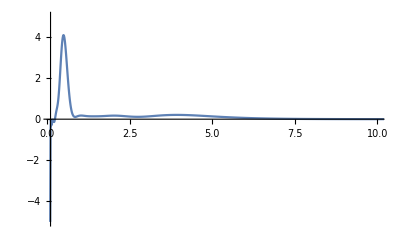

```mathematica
ListLinePlot[sdata, PlotRange->{{0.1,10},{-5,5}}]
```

```mathematica
ListLinePlot[{sdata1,sdata, sdatadiff},PlotRange->{{0.1,1},{-1,5}}, PlotMarkers->{Automatic, 10}]
```

-Graphics-

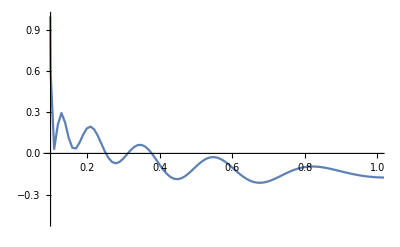

```mathematica
ListLinePlot[sdatadiff,PlotRange->{{0.1,1},{-0.5,1}}]
```